```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
Get[NotebookDirectory[]<>"QBMMlibpub.wl"];
Get[NotebookDirectory[]<>"TimeSteppers.wl"];
(*Needs["CellsToTeX`"];*)
```

```mathematica
(* Input parameters *)
case="linear2d";

ClearAll[ro,ttt];
If[case=="linear1d",
	Cp0=1;
	Toneperiod=1;
	(*eqn=rd+r-r^2==2;*)
	eqn=rd==4r-2 r^2;
	vars={{r},rd};
	(*tmax=5;
	sol=First[rr[tt]/.NDSolve[{rr'[tt]==4rr[tt](*-1 rr[tt]^(-1/2)*)-2 rr[tt]^2,rr[0]==0.5},rr[tt],{tt,0,tmax}]]
	Plot[sol/.tt->t,{t,0,tmax},PlotRange->All]*)
];
If[case=="linear2d",
	Cp0=1;
	Cp[t_]:=Cp0;
	Toneperiod=3.4 (1/Cp0)^0.75;
	eqn=rdd+rd+r==0;
	vars={{r,rd},rdd};
];
If[case=="nonlinear2d",
	γ=1.4;
	Cp0=1;
	Toneperiod=3.4  (1/Cp0)^0.75;
	Cp[t_]:=Cp0;
	(*Cp[t_]:=If[t<Toneperiod,Cp0 Sin[2 Pi t/Toneperiod]+1,1];*)	
	ro=1;
	eqn=r rdd+(3/2)rd^2==(ro/r)^(3 γ)-Cp[ttt];
	vars={{r,rd},rdd};
];
If[case=="nonlinear3d",
	γ=1.4;
	Cp0=0.1;
	Toneperiod=3.4  (1/Cp0)^0.75;
	(*Cp[t_]:=Cp0;*)
	Cp[t_]:=If[t<Toneperiod,Cp0 Sin[2 Pi t/Toneperiod]+1,1];
	eqn=r rdd+(3/2)rd^2==(ro/r)^(3 γ)-Cp[ttt];
	vars={{r,rd,ro},rdd};
];

dim=Length[vars[[1]]];
{coefs,exps}=TransportTerms[eqn,vars]
```

{{-c[2],-c[2],c[1]},{{1+c[1],-1+c[2]},{c[1],c[2]},{-1+c[1],1+c[2]}}}

```mathematica
Nperiod=3;
T=Nperiod Toneperiod;

dt=1.  10^-5;dt0=dt;
dtmin=dt;dtmax=10000dt;
tol=10 10^-6;

ClearAll[P1,P12PDF];
If[dim==1,
	n={3};
	perms={1};
	μ1=0.5;σ1=0.1;
	P1=NormalDistribution[μ1,σ1];
	GenMoment[idx_]:=Moment[P1,idx[[1]]];
];
If[dim==2,
	n={2,2};
	perms={12};
	(*perms={12,21};*)

	μ1=1.;σ1=0.1;
	P1=LogNormalDistribution[Log[μ1],σ1];
	μ2=0;σ2=Sqrt[0.05];
	P2=NormalDistribution[μ2,σ2];		
	P12PDF=ProductDistribution[P1,P2];
	P12PDF = BinormalDistribution[{1,1},{0.5,1},0.5];
	GenMoment[idx_]:=Moment[P12PDF,idx];
];
If[dim==3,
	n={2,2,3};
	perms={12};
	(*perms={12,21};*)
	μ2=0;σ2=Sqrt[0.05];
	P2=NormalDistribution[μ2,σ2];

	μ3=1.;σ3=0.1;
	P3=LogNormalDistribution[Log[μ3],σ3];
	Moment3=Table[Moment[P3,i-1],{i,2n[[3]]}];
	{xi3,w3}=Wheeler[Moment3];
	(*xi3={1};w3={1};*)

	Do[
		μ1=xi3[[i]];σ1=0.1;
		P1[i]=LogNormalDistribution[Log[μ1],σ1];
		(*P12PDF[i]=ProductDistribution[P1[i],P2];*)
		P12PDF[i]=BinormalDistribution[{μ1,μ2},{σ1,σ2},0.1];
	,{i,n[[3]]}];
	GenMoment[idx_]:=Moment[P12PDF[idx[[3]]+1],{idx[[1]],idx[[2]]}];
	P123PDF=ProductDistribution[P1,P2,P3];
];

nperm=Length[perms];
method="CHYQMOM" ;(* Options: "AQMOM", "QMOM", "HYQMOM", "CQMOM", "CHYQMOM"*)
ks=MomentIndex[n,method(*,nperm*)];
If[dim==3&&NumberQ[γ],ksp={{3,0,0},{2,1,0},{3,2,0},{3(1-γ),0,3γ}}];
```

```mathematica
F[moms_,t_]:=Module[{rhs,mom,mout,rout},
	Do[
		{w,xi}=MomentInvert[moms,ks,Method->method,Permutation->perms[[i]]];
		(*rhs[i]=ComputeRHS[w,xi,ks,{coefs,exps}];*)
		rhs[i]=ComputeRHS[w,xi,ks,{coefs/.ttt->t,exps},Conditioning->xi3];
		mom[i]=Project[w,xi,ks];
	,{i,nperm}];
	mout=Sum[mom[i],{i,nperm}]/nperm;
	rout=Sum[rhs[i],{i,nperm}]/nperm;
	Return[{mout,rout},Module];
];

TotalMoments[moms_,idx_]:=Sum[w3[[l]] xi3[[l]]^idx[[3]] MomentFind[moms,ks,{idx[[1]],idx[[2]],l-1}],{l,n[[3]]}];
```

```mathematica
(* ic *)moms=Map[GenMoment,ks];

sol={};ts={};dets={};abscissa={};fullmoms={};
t=0;dt=dt0;
Monitor[While[t≤T,
	{moms,mome,e}=RK23[moms,F,t,dt];
	AppendTo[sol,moms];
	AppendTo[ts,t];
	AppendTo[abscissa,OutAbscissa[xi]];

	(*fullmom=Table[TotalMoments[moms,ks[[i]]],{i,Length[ks]}];
	AppendTo[fullmoms,fullmom];*)
	
	t=t+dt;
	dt=dt Min[Max[Sqrt[tol/(2 e)],0.3],2.];
dt=Min[Max[0.9 dt,dtmin],dtmax];

If[Norm[moms]>10^5,Print["Crash ",100 t/T];Break[]];
	(*If[e<10^-16&&t>0.1T,Print["Error zero, stationary point likely reached. Aborting."];Break[]];*)
];
,TableForm[{{"Time",100t/T},{"δt",dt/dt0},{"Moments",Max[Abs[moms]]},{t,T}}]
]//AbsoluteTiming
Length[ts]
```

{2.06002,Null}

296

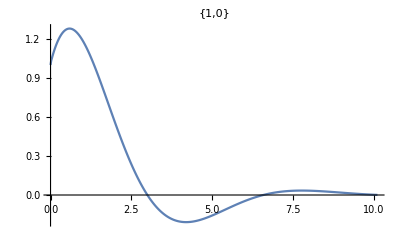
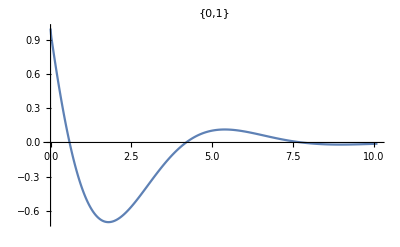
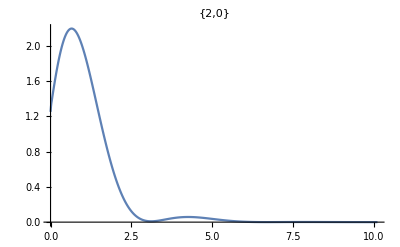
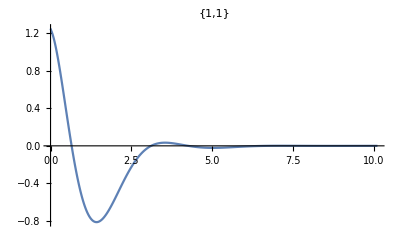
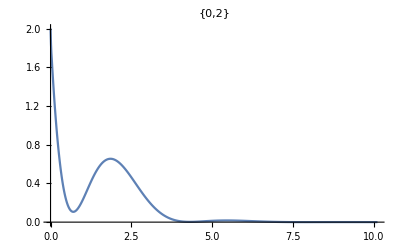

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[Thread[{ts,sol[[All,i]]}],Joined->True,PlotRange->All,PlotLabel->ks[[i]]]]
]
,{i,1,Length[moms]}]
plots
```

```mathematica
(* Verify with Monte Carlo *)
If[
	dim==3,
	NcasesRRd=50;
	cases=RandomVariate[P123PDF,Ncases];

	NcasesRo=50;
	casesRo=RandomVariate[P3,NcasesRo]//Sort;
	Do[casesRRd[i]=RandomVariate[ProductDistribution[LogNormalDistribution[Log[casesRo[[i]]],σ1],P2],NcasesRRd],{i,NcasesRo}];
	cases=Flatten[Table[{casesRRd[kk][[i,1]],casesRRd[kk][[i,2]],casesRo[[kk]]},{i,NcasesRRd},{kk,NcasesRo}],1];
	Ncases=Length[cases];
,
	Ncases=1000;
	cases=RandomVariate[P12PDF,Ncases];
	cases=Table[{cases[[i,1]],cases[[i,2]]},{i,Ncases}];
];

Clear[t];
Nt=100;ts2=Table[i,{i,0,T,T/Nt}];
ts2=ts;Nt=Length[ts2];

If[case=="linear",
	β=2/Rey;ω2= 2 γ Ca;
	myr=ParallelTable[
	r[t]/.(NDSolve[
{r''[t] == -2 β r'[t]-ω2 r[t]-Cp[t],r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,Ncases}];
];
If[case=="linear2d",
	myr=ParallelTable[
r[t]/.(NDSolve[
{r''[t]+r'[t]+r[t]==0,r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],{t,0,T}]//First//First),
{i,Ncases}];
];
If[case=="nonlinear3d",
	myr=ParallelTable[
r[t]/.(NDSolve[
{r[t]r''[t]+3/2 r'[t]^2 ==(cases[[i,3]]/r[t])^(3 γ)-Cp[t],r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,Ncases}];
];
mydr=ParallelTable[D[myr[[i]],t],{i,Ncases}];

If[dim==2,
	P=Table[
		Table[
			{myr[[j]]/.{t->ts2[[i]]},
			mydr[[j]]/.{t->ts2[[i]]}}
		,{j,Ncases}]
	,{i,Nt}];

	mcmoms=ParallelTable[Table[{ts2[[i]],Moment[P[[i]],ks[[j,1;;2]]]},{i,Nt}],{j,Length[ks]}];
	qmoms=Table[Thread[{ts,sol[[All,i]]}],{i,Length[moms]}];

	plots0={};
	Do[
		If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
			AppendTo[plots0,ListPlot[{qmoms[[i]],mcmoms[[i]]},Joined->True,PlotRange->All,PlotLabel->ks[[i]],AxesLabel->{"t","Moment"}]]
		];
	,{i,Length[moms]}];
];

If[dim==3,
	P=Table[
		Table[
		{
		myr[[j]]/.{t->ts2[[i]]},
		mydr[[j]]/.{t->ts2[[i]]},
		cases[[j,3]]
		}
		,{j,Ncases}]
	,{i,Nt}];
	mcmoms=ParallelTable[Table[{ts2[[i]],Moment[P[[i]],ks[[j,1;;3]]]},{i,Nt}],{j,Length[ks]}];
	mcmomssp=ParallelTable[Table[{ts2[[i]],Moment[P[[i]],ksp[[j,1;;3]]]},{i,Nt}],{j,Length[ksp]}];

	plots1={};
	Do[
		If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
			AppendTo[plots1,ListPlot[{Thread[{ts,fullmoms[[All,i]]}],mcmoms[[i]]},Joined->True,PlotRange->All,PlotLabel->ks[[i]],AxesLabel->{"t","Moment"}]]
		];
	,{i,Length[moms]}];

	plots2={};
	Do[
		AppendTo[plots2,ListPlot[{Thread[{ts,spsol[[All,i]]}],mcmomssp[[i]]},Joined->True,PlotRange->All,PlotLabel->ksp[[i]],AxesLabel->{"t","Moment"}]]
	,{i,Length[momsp]}];
];
```

00

```mathematica
dir="/Users/spencerbryngelson/Documents/Caltech/Research/docs_papers/paper_QBMMlib/D/verification/linear_2d/";
Do[
	OutAll=Flatten[{{{"ColumnX","ColumnY"}},qmoms[[i]]},1];
	Export[dir<>"MOM_"<>ToString[ks[[i,1]]]<>ToString[ks[[i,2]]]<>"mom.csv",OutAll,"Table"];
,{i,Length[qmoms]}];
```

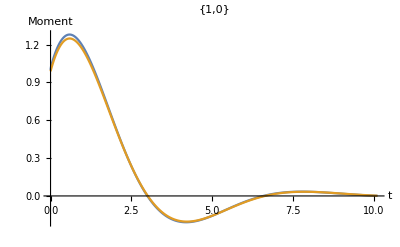
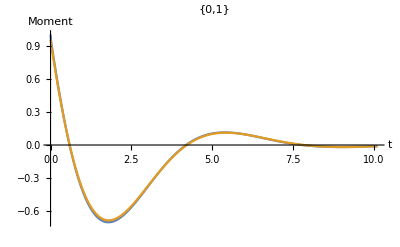
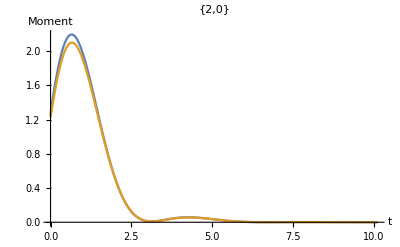
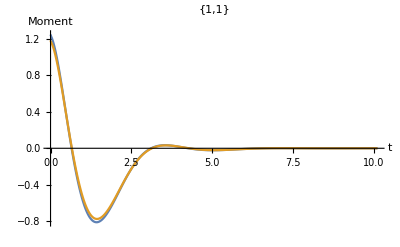
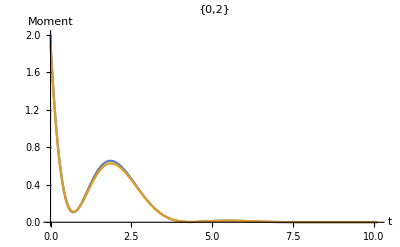

```mathematica
plots0
```

```mathematica
If[dim==2,
	xdat=abscissa[[All,All,1]];
	ydat=abscissa[[All,All,2]];
	xmax=1.2Max[xdat];xmin=If[Min[xdat]<0,1.2 Min[xdat],Min[xdat]/1.2];
	ymax=1.2Max[ydat];ymin=If[Min[ydat]<0,1.2Min[ydat],Min[ydat]/1.2];

	plts=ParallelTable[
	Show[
	SmoothDensityHistogram[P[[i]],PlotRange->{{xmin,xmax},{ymin,ymax},All}],
	ListPlot[abscissa[[i]],PlotStyle->Red,PlotRange->{{xmin,xmax},{ymin,ymax}}]]
	,{i,1,Length[P],10}];
	vid=ListAnimate[plts];
];
vid
(*Export["~/Desktop/movie.avi",vid]*)
```

```mathematica
If[dim==3,
	myn=100;
	plottingfac=1;
	myts=Table[ts[[i]],{i,Length[abscissa],Floor[Length[abscissa]/myn]}];
	Do[myabscissa[j]=Table[abscissa[[i,j]],{i,1,Length[abscissa],Floor[Length[abscissa]/N[myn]]}],{j,n[[3]]}];
	Do[
		xdat[j]=myabscissa[j][[All,All,1]];
		ydat[j]=myabscissa[j][[All,All,2]];
		xmax[j]=If[Max[xdat[j]]>0,1.2 Max[xdat[j]],0.8 Max[xdat[j]]];
		xmin[j]=If[Min[xdat[j]]<0,1.2 Min[xdat[j]],0.8 Min[xdat[j]]];
		ymax[j]=If[Max[ydat[j]]>0,1.2 Max[ydat[j]],0.8 Max[xdat[j]]];
		ymin[j]=If[Min[ydat[j]]<0,1.2Min[ydat[j]],0.8 Min[ydat[j]]];
	,{j,n[[3]]}];
	xminF=Min[Table[xmin[j],{j,n[[3]]}]];
	xmaxF=Max[Table[xmax[j],{j,n[[3]]}]];
	yminF=Min[Table[ymin[j],{j,n[[3]]}]];
	ymaxF=Max[Table[ymax[j],{j,n[[3]]}]];

	dat3d=Table[Flatten[Table[Table[Flatten[{xi3[[j]],myabscissa[j][[k,i]]},1],{i,Length[myabscissa[j][[k]]]}],{j,n[[3]]}],1],{k,Length[myabscissa[1]]}];

	anim1=ListAnimate[ParallelTable[
		ListPlot[
			Table[myabscissa[j][[i]],{j,n[[3]]}],PlotRange->{{xminF//Re,xmaxF//Re},{yminF//Re,ymaxF//Re}},AxesLabel->{"R","V"}]
	,{i,1,Length[myabscissa[1]]/plottingfac}]
		];

	anim2=ListAnimate[
		ParallelTable[
			ListPointPlot3D[dat3d[[i]],PlotRange->{{0.9Min[xi3],1.1Max[xi3]},{xminF//Re,xmaxF//Re},{yminF//Re,ymaxF//Re}},
			AxesLabel->{"Ro","R","V"}]
		,{i,Length[dat3d]/plottingfac}]
	];

];
(*Export["~/Desktop/anim2.avi",anim,AnimationRunTime->6];*)
```